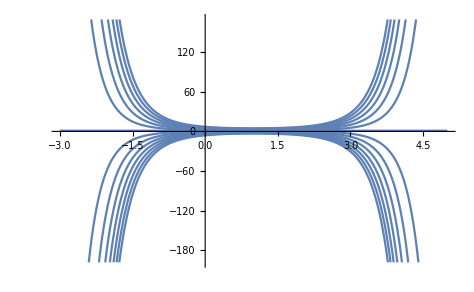
```mathematica
solution = DSolve[y'[t]==(1-t)(1-y[t]), y[t], t]

{{y[t]->1+ⅇ^(-t+t^2/2) C[1]}}

f[t_]=y[t]/. solution⟦1⟧

F[t_]=Table[f[t]/.C[1]->j, {j, -4.0, 4.0}]

Plot[{F[t]}, {t, -3.0, 5.0}]

-Graphics-
```